## 1. SN/hopf

```mathematica
xdot=y;
ydot=μ1+μ2 y+x^2 + x y;
J=D[{xdot,ydot},{{x,y}}];
```

```mathematica
xsolns=Solve[{xdot==0,ydot==0},{x,y}];
MatrixForm[xsolns]
```

(x→-ⅈ √μ1 | y→0
x→ⅈ √μ1 | y→0)

```mathematica
xsolns/.{μ1->-1}
```

{{x→1,y→0},{x→-1,y→0}}

Alternate Form

```mathematica
udot=v;
vdot=ν1+u^2+ϵ(ν2 v+u v);
G=D[{udot,vdot},{{u,v}}];
```

```mathematica
usolns=Solve[{udot==0,vdot==0},{u,v}]
```

{{u→-ⅈ √ν1,v→0},{u→ⅈ √ν1,v→0}}

Find the eigenvalues at the first steady state:

```mathematica
Λ1=Eigenvalues[J/.xsolns[[1]]];
Λ2=Eigenvalues[J/.xsolns[[2]]];
Λ=Λ2;
StandardForm[MatrixForm[Λ]]
V=Eigenvectors[J/.{x->I*Sqrt[μ1],y->0}];
StandardForm[MatrixForm[Simplify[V/.{μ1->-1,μ2->-8}]]]//N
Λ=Flatten[Λ];
```

(1/2 (ⅈ √μ1-√(8 ⅈ √μ1+(-ⅈ √μ1-μ2)^2)+μ2)
1/2 (ⅈ √μ1+√(8 ⅈ √μ1+(-ⅈ √μ1-μ2)^2)+μ2))

(-0.113999 | 1.
-4.386 | 1.)

Some plotting functions

```mathematica
implot[f_,domain_]:=ParametricPlot[{Re[f],Im[f]},
domain,
AxesLabel->{"real","imaginary"}
]
implot2[f_,domain_]:=
(
p1=Plot[
Re[f],
domain,
PlotLegends->{"real"},
PlotStyle->{Red},
Mesh->All
];
p2=Plot[
Im[f],
domain,
PlotLegends->{"imaginary"},
PlotStyle->{Blue}
];
Return[Show[p1,p2,AxesLabel->{domain[[1]]}]];
)
```

Find borders of the μ_2 region in which imaginary λ values exist:

For the first SS:

```mathematica
borders1=Solve[-8 ⅈ √μ1+(ⅈ √μ1-μ2)^2==0,μ2];
borders1/.{μ1->-1}//N
```

{{μ2→-1.-2.82843 ⅈ},{μ2→-1.+2.82843 ⅈ}}

These have nonzero imaginary part, which we can’t do.

For the second SS:

```mathematica
borders2=Solve[8 ⅈ √μ1+(-ⅈ √μ1-μ2)^2==0,μ2];
MatrixForm[Simplify[
Refine[borders2,μ1<0]
]]
```

(μ2→√-μ1-(2-2 ⅈ) μ1^(1/4)
μ2→√-μ1+(2-2 ⅈ) μ1^(1/4))

```mathematica
MatrixForm[μ2/.Refine[borders2,μ1<0]]
```

(-ⅈ (ⅈ √-μ1-(2+2 ⅈ) μ1^(1/4))
-ⅈ (ⅈ √-μ1+(2+2 ⅈ) μ1^(1/4)))

```mathematica
((2+2 ⅈ) μ1^(1/4))^2
```

8 ⅈ √μ1

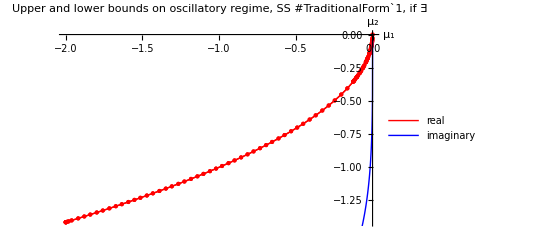

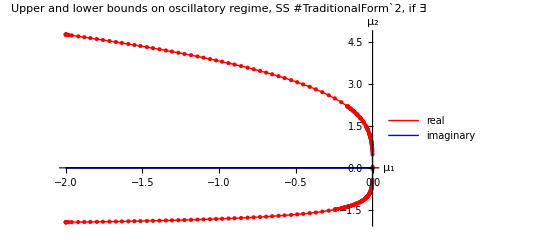

```mathematica
For[i=1,i<3,i++,
borders={borders1,borders2}[[i]];
pl=implot2[μ2/.borders,{μ1,-2,0}];
Print[Show[pl,PlotLabel->StringForm["Upper and lower bounds on oscillatory regime, SS #``, if ∃",i],
AxesLabel->{"μ_1","μ_2"}]];
]
```

Only the second SS has real bounds on the oscillatory regime.

```mathematica
For[i=1,i<3,i++,
eigs={Λ1,Λ2}[[i]];
re=Re[eigs];
im=Im[eigs];
(*re=Re[x/.xsolns[[2]]];*)
(*im=Im[x/.xsolns[[2]]];*)
Print[Plot3D[{
re,
im,
(*If[im==0,∞,im],*)
0
},
{μ1,-2,0},{μ2,-4,6},AxesLabel->Automatic,Mesh->None,
PlotStyle->{
{Red,Specularity[White,100],Opacity[.5]},
{Green,Specularity[White,100],Opacity[.5]},
{Blue,Opacity[.5]}
},
ImageSize->Large,
PlotLabel->StringForm["Re[λ_1] (red) and Im[λ_1] (green) at SS #``, with zero-plane (blue)",i]
]];
]
```

-Graphics3D-

-Graphics3D-

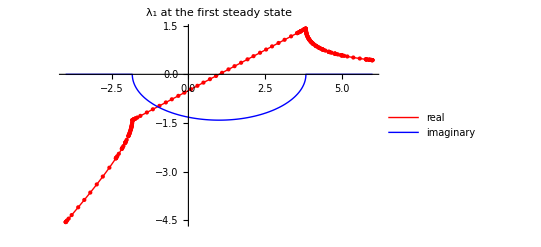

```mathematica
pl=implot2[Λ[[1]]/.{μ1->-1},{μ2,-4,6}];
Show[pl,PlotLabel->"λ_1 at the first steady state"]
```

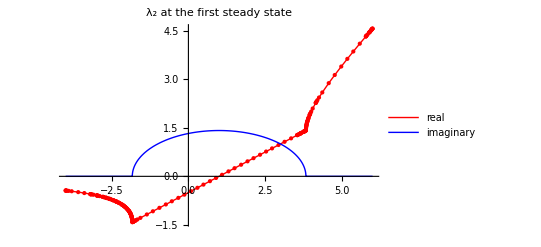

```mathematica
pl=implot2[Λ[[2]]/.{μ1->-1},{μ2,-4,6}];
Show[pl,PlotLabel->"λ_2 at the first steady state"]
```

```mathematica
allPlots={};
For[i=1,i<4,i++,
For[j=1,j<3,j++,
u1={-8,-1}[[j]];
u2={-4,1,6}[[i]];
params={μ1->u1,μ2->u2};
xmin=-4;xmax=4;ymin=-2;ymax=2;
xres=yres=128;
cmap="BeachColors";

(*A dense vector-flow plot:*)
vplot=LineIntegralConvolutionPlot[
{{xdot,ydot}/.params,{Automatic,xres,yres}},
{x,xmin,xmax},{y,ymin,ymax},
StreamColorFunction->Hue,
ColorFunction->cmap,(*From ColorData["Gradients"]*)
LineIntegralConvolutionScale->3,
LightingAngle->0,
AxesLabel->{"x","y"}
];
(*vplot=Plot[{},{x,-1,1}];*)

(*A less-dense explicit vector field (quiver) plot:*)
values=Flatten[Table[
(* Calculate all the vector norms, for making a color bar later.*)
Table[
Sqrt[xdot^2+ydot^2]/.params/.{x->xval,y->yval},
{xval,xmin,xmax}
],
{yval,ymin,ymax}
]];
splot=StreamPlot[{xdot,ydot}/.params,
{x,xmin,xmax},{y,ymin,ymax},
StreamColorFunction->(ColorData[cmap][#i]&),
StreamStyle->{White,Thick},
StreamPoints->16,
(*StreamPoints->{Tuples[Range[-3,3,0.2],2],Automatic,10},*)
LightingAngle->0,
AxesLabel->{"x","y"},
PlotLegends->{BarLegend[
{cmap,{Min[values],Max[values]}},
LegendLabel->(SqrtBox[(ẋ)^2+(ẏ)^2]//DisplayForm)
]}
];
(*Print[splot];*)

(*Scatter plot at the fixed points:*)
xx=x/.xsolns/.params;
    yy=y/.xsolns/.params;
data=Transpose@{xx,yy};
listplot=ListPlot[
data,
PlotStyle->{PointSize[Large],White},
AxesLabel->{"x","y"}
];

(*Combine them all in one plot:*)
title=StringForm["μ_1=`` μ_2=``",u1,u2];
Print[title];
shown=Show[
vplot,listplot,splot,
ImageSize->Medium,
AxesLabel->{"x","y"},
PlotLabel->title
];
(*Print[shown];*)
AppendTo[allPlots,shown];
]
]
allPlots
```

μ_1=-8 μ_2=-4

μ_1=-1 μ_2=-4

μ_1=-8 μ_2=1

μ_1=-1 μ_2=1

μ_1=-8 μ_2=6

μ_1=-1 μ_2=6

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}